```mathematica
filesAR=FileNames["/home/carla/GDC/CONF/MUR/GDC_Conf_AR_MUR_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/CONF/MUR/GDC_Conf_BR_MUR_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]];
zAR=confAR[[All,2]][[All,1]];
fAR=confAR[[All,3]][[All,1]];
```

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.00642674,0.0042735,0.0625,0.0232558,0.00487805,0.0232558,1.}

{0.00540125,0.00328668,0.0614909,0.0226576,0.00304249,0.0229253,1.}

{0.724784,0.624806,0.968222,0.949845,0.453182,0.971973,1}

```mathematica
sList={1,2,3,4,5,6,7,8};
sList2={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran]
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&, ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&, ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

{{1,0.00642674},{2,0.00642674},{3,0.0625},{4,0.0625},{5,0.00884956},{6,0.0232558},{7,1.},{8,1.}}

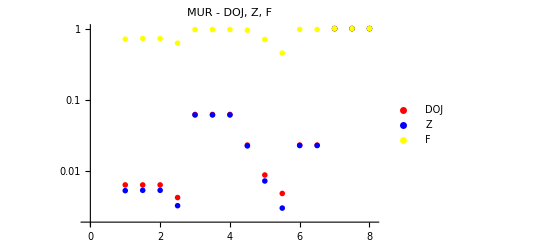

```mathematica
PlotAllParts=ListLogPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotRange->{{-0.1,8.1},All},PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"MUR - DOJ, Z, F", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/CONF/MUR/"];
Put[Union[dojPAR,dojPBR],"MUR_DOJ.txt"]
Put[Union[zPAR,zPBR],"MUR_Z.txt"]
Put[Union[fPAR,fPBR],"MUR_F.txt"]
Export["MUR.jpeg",PlotAllParts,ImageSize->800, ImageResolution->300]
```

MUR.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{-0.001, 0.084},  PlotLabel->"MUR - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["MUR_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```